## Longform

Restart from beginning

```mathematica
SetDirectory["/Users/smgomez/projects/gitrepos/PDACperturbations/data"];
KlaegerData=Import["/Users/smgomez/projects/gitrepos/PDACperturbations/data/KlaegerScience2017/Klaeger_Science_2017 Supplementary Table 2 Target Lists.xlsx","XLSX"];
```

```mathematica
kinobeads=KlaegerData[[3]]
```

{{Drug,Lysate,Beads,Gene Name,Relative Intensity DMSO,Relative Intensity 3 nM,Relative Intensity 10 nM,Relative Intensity 30 nM,Relative Intensity 100 nM,Relative Intensity 300 nM,6,Bottom,Top,Inflection,EC50,EC50 Standard Error,Correction Factor,Apparent Kd,R2,BIC,Target Classification},5915,{1}}
 |  |  |  |

Want to make sure the data I have from Isaac has rows being drugs at a specific dose and a corresponding set of columns describe standardized kinobead measurements. If this corresponds to what Isaac made, we are good to go with downstream analyses using this data.

May also want to make a version that just has the raw, non-standardized values. It may be useful if we want to incorporate other kinobead vectors in the future.

```mathematica
kinobeads[[1]]
```

{Drug,Lysate,Beads,Gene Name,Relative Intensity DMSO,Relative Intensity 3 nM,Relative Intensity 10 nM,Relative Intensity 30 nM,Relative Intensity 100 nM,Relative Intensity 300 nM,Relative Intensity 1000 nM,Relative Intensity 3000 nM,Relative Intensity 30000 nM,DMSO Intensity,Intensity Type,Slope,Bottom,Top,Inflection,EC50,EC50 Standard Error,Correction Factor,Apparent Kd,R2,BIC,Target Classification}

Want the concentrations to be in terms of μM, so our 30,000 nM will be listed as 30 in our concentration column (as Isaac did originally).

```mathematica
kinobeads[[2]]
```

{Abemaciclib,4 cell line mix,Kinobeads,AAK1,1.,0.905556,0.791054,0.738292,0.639565,0.323354,0.181984,0.0634211,0.0571028,1.363×10^8,Normalized LFQ intensity,0.773714,0.00909176,0.957905,151.289,151.289,45.697,0.673073,101.828,0.985386,-20.5035,High confidence}

In the spreadsheet, rows are gene & drug-based - it gives the response of a gene (named in column 4) to a drug (named in column 1) at multiple doses (columns 6-13).

```mathematica
kinobeads[[1,{1,4,6,7,8,9,10,11,12,13}]]
```

{Drug,Gene Name,Relative Intensity 3 nM,Relative Intensity 10 nM,Relative Intensity 30 nM,Relative Intensity 100 nM,Relative Intensity 300 nM,Relative Intensity 1000 nM,Relative Intensity 3000 nM,Relative Intensity 30000 nM}

Pull out the kinobead responses for AAK1 for all drugs and doses.

```mathematica
kb=kinobeads[[2;;,{1,4,6,7,8,9,10,11,12,13}]]
```

{{Abemaciclib,AAK1,0.905556,0.791054,0.738292,0.639565,0.323354,0.181984,0.0634211,0.0571028},5914,{Y-39983,TAOK1,1.23274,4,0.716763,0.789106,0.}}
 |  |  |  |

```mathematica
kb=Dataset[kb]
```

Dataset[<>]

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/DataReshape.m"]
```

```mathematica
kb=kb[All,<|"Drug"->1,"Gene Name"->2,"3 nM"->3,"10 nM"->4,"30 nM"->5,"100 nM"->6,"300 nM"->7,"1000 nM"->8,"3000 nM"->9,"30000 nM"->10|>]
```

Dataset[<>]

```mathematica
KlaegerLong = ToLongForm[kb,{"Drug","Gene Name"}]
```

Dataset[<>]

```mathematica
KlaegerLong=KlaegerLong[All,KeyMap[Replace["Variable"->"Dose (uM)"]]]
```

Dataset[<>]

Using the long version of the data to get a feel for small numbers.

```mathematica
DeleteCases[KlaegerLong[All,"Value"],0.0]//Min
```

Min[0.000481786,NA]

```mathematica
minValue=KlaegerLong[Select[#"Value">0.0&],"Value"]//Min
```

0.000481786

Let’s set the pseudocount to a value 1/4 that of the minimum measured value.

```mathematica
pseudoCount=minValue/4
```

0.000120447

```mathematica
Log2[pseudoCount]
```

-13.0193

```mathematica
Log2[minValue]
```

-11.0193

```mathematica
KlaegerLong=ReplaceAll[KlaegerLong,{0.0->pseudoCount}]
```

Dataset[<>]

```mathematica
KlaegerLong=ReplaceAll[KlaegerLong,{"NA"->pseudoCount}]
```

Dataset[<>]

Now log2 transform

```mathematica
KlaegerLong=KlaegerLong[All,{"Value"->Log2}]
```

Dataset[<>]

```mathematica
KlaegerLong=ReplaceAll[KlaegerLong,{"3 nM"->0.003,"10 nM"->0.01,"30 nM"->0.03,"100 nM"->0.1,"300 nM"->0.3,"1000 nM"->1,"3000 nM"->3,"30000 nM"->30}]
```

Dataset[<>]

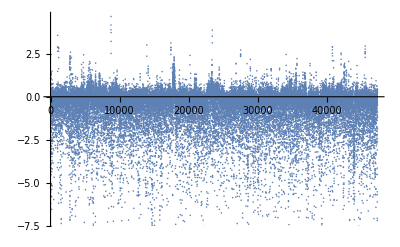

```mathematica
KlaegerLong[ListPlot,"Value"]
```

```mathematica
Export["/Users/smgomez/projects/gitrepos/PDACperturbations/data/KlaegerScience2017/KlaegerLong.csv",KlaegerLong,"CSV"]
```

/Users/smgomez/projects/gitrepos/PDACperturbations/data/KlaegerScience2017/KlaegerLong.csv

After log transforming...
Also need to scale appropriately

## Wideform

```mathematica
KlaegerWide=ToWideForm[KlaegerLong,{"Drug","Dose (uM)"},"Gene Name","Value"]
```

Dataset[<>]

```mathematica
KlaegerWide=ReplaceAll[KlaegerWide,{Missing[]->Log2[pseudoCount]}]
```

Dataset[<>]

Just export this version for now.

```mathematica
Export["/Users/smgomez/projects/gitrepos/PDACperturbations/data/KlaegerScience2017/KlaegerWide.csv",KlaegerWide,"CSV"]
```

/Users/smgomez/projects/gitrepos/PDACperturbations/data/KlaegerScience2017/KlaegerWide.csv